```mathematica
t={0,0,0,19,72,156,266,396,540,695,860,1032,1219,1412,1608,1806,2007,2209,2412,2616,2820,3025,3230,3436,3642,3848,4054,4260,4467,4673,4880,5086,5293,5499,5706,5913,6120,6326,6533,6739,6945,7151,7357,7563,7769,7975,8181,8387,8593,8799,9005,9211,9418,9624,9830,10041,10259,10476,10694,10911,11129,11346,11564,11781,11999,12217,12435,12653,12871,13090,13308,13527,13745,13964,14182,14401,14620,14838,15057,15276,15494,15713,15932,16151,16369,16588,16807,17026,17244,17463,17682,17900,18119,18338,18557,18776,18994,19213,19432,19651,19869,20088,20307,20526,20744,20963,21182,21401,21619,21838,22057,22276,22494,22713,22932,23151,23369,23588,23807,24026,24244,24463,24682,24901,25119,25338,25557,25776,25995,26213,26432,26651,26870,27088,27307,27526,27745,27963,28182,28401,28620,28839,29057,29276,29495,29714,29933,30151,30370,30589,30808,31027,31245,31464,31683,31902,32121,32339,32558,32777,32996,33214,33433,33652,33871,34090,34308,34527,34746,34965,35183,35402,35621,35840,36059,36277,36496,36715,36933,37152,37371,37590,37808,38027,38246,38465,38683,38902,39121,39340,39559,39778,39996,40215,40434,40653,40871,41090,41309,41528,41747,41966,42184,42403,42622,42841,43060,43279,43498,43717,43936,44154,44373,44592,44811,45030,45249,45468,45687,45906,46124,46343,46562,46781,47000,47219,47438,47657,47876,48095,48314,48533,48752,48971,49189,49408,49627,49846,50065,50284,50503,50722,50941,51159,51378,51597,51816,52035,52254,52473,52692,52911,53129,53348,53567,53786,54005,54224,54443,54662,54881,55099,55318,55537,55756,55975,56194,56413,56632,56850,57069,57288,57507,57726,57945,58164,58383,58602,58821,59040,59259,59477,59696,59915,60134,60353,60572,60791,61010,61229,61448,61667,61886,62105,62324,62543,62762,62981,63200,63420,63639,63858,64077,64296,64515,64734,64953,65172,65391,65610,65829,66048,66267,66486,66705,66924,67143,67361,67580,67799,68018,68237,68456,68675,68893,69112,69331,69550,69769,69988,70207,70426,70645,70864,71083,71301,71520,71739,71958,72177,72396,72615,72834,73053,73272,73491,73710,73929,74148,74367,74586,74805,75024,75243,75462,75681,75900,76119,76338,76557,76776,76995,77214,77433,77652,77871,78090,78309,78528,78747,78966,79185,79404,79623,79842,80061,80281,80500,80719,80938,81157,81376,81595,81814,82033,82252,82471,82689,82908,83126,83345,83564,83783,84001,84220,84439,84658,84877,85096,85315,85534,85753,85972,86191,86410,86629,86848,87067,87285,87504,87723,87942,88161,88380,88598,88816,89035,89253,89472,89690,89908,90127,90345,90563,90781,90999,91217,91435,91654,91872,92091,92310,92529,92747,92966,93185,93403,93622,93841,94060,94278,94497,94711,94910,95093,95261,95415,95556,95684,95800,95904,95996,96079,96151,96216,96274,96325,96372,96414,96452,96488,96520,96550,96576};
```

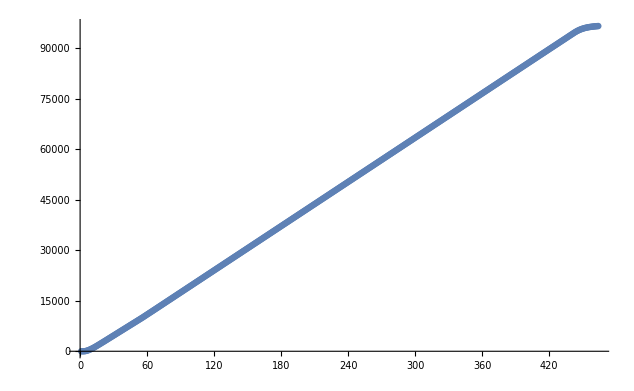

```mathematica
ListPlot[t]
```

```mathematica
LinearModelFit[t,x,x]
```

FittedModel[-737.185+105.382 x]

```mathematica
t2={0,0,4,36,102,201,323,463,617,783,957,1142,1339,1540,1743,1950,2157,2366,2576,2786,2996,3207,3418,3629,3841,4052,4264,4475,4687,4899,5111,5322,5534,5746,5958,6170,6381,6593,6805,7017,7229,7441,7653,7865,8077,8288,8500,8712,8924,9136,9348,9560,9772,9984,10196,10419,10643,10867,11091,11314,11538,11762,11985,12209,12433,12657,12880,13104,13328,13551,13775,13999,14222,14446,14670,14894,15117,15341,15565,15789,16012,16236,16460,16684,16907,17131,17355,17578,17802,18025,18249,18473,18696,18920,19143,19367,19591,19814,20038,20261,20485,20709,20932,21156,21379,21603,21827,22050,22274,22497,22721,22945,23168,23392,23615,23839,24062,24286,24509,24733,24956,25180,25403,25627,25850,26074,26297,26521,26744,26968,27191,27415,27638,27862,28085,28309,28532,28756,28979,29203,29426,29650,29873,30097,30321,30544,30767,30991,31214,31438,31661,31885,32108,32332,32555,32779,33003,33226,33450,33673,33897,34120,34344,34567,34791,35014,35238,35461,35685,35909,36132,36356,36579,36803,37026,37250,37473,37697,37921,38144,38368,38591,38815,39039,39262,39486,39709,39933,40157,40381,40604,40828,41051,41275,41499,41722,41946,42169,42393,42616,42840,43064,43287,43511,43735,43958,44182,44405,44629,44853,45076,45300,45524,45747,45971,46195,46419,46642,46866,47090,47313,47537,47760,47984,48208,48431,48655,48879,49103,49326,49550,49774,49997,50221,50445,50668,50892,51115,51339,51563,51786,52010,52233,52457,52681,52904,53128,53352,53575,53799,54023,54246,54470,54693,54917,55141,55364,55588,55811,56035,56259,56482,56706,56930,57153,57377,57600,57824,58048,58271,58495,58719,58942,59166,59390,59614,59837,60061,60285,60508,60732,60956,61180,61403,61627,61851,62075,62299,62522,62746,62970,63193,63417,63641,63864,64088,64312,64535,64759,64983,65206,65430,65654,65877,66101,66324,66548,66771,66995,67219,67442,67666,67889,68113,68336,68560,68783,69007,69230,69454,69677,69901,70124,70348,70571,70795,71019,71242,71466,71690,71913,72137,72360,72584,72808,73031,73255,73479,73702,73926,74149,74373,74597,74820,75044,75268,75491,75715,75939,76162,76386,76610,76833,77057,77281,77504,77728,77952,78175,78399,78623,78846,79070,79293,79517,79740,79964,80187,80411,80634,80858,81081,81305,81528,81752,81975,82199,82422,82645,82869,83092,83316,83539,83763,83987,84210,84434,84657,84881,85104,85328,85552,85775,85999,86222,86446,86669,86893,87117,87340,87564,87787,88011,88235,88458,88681,88905,89128,89351,89574,89797,90021,90244,90466,90689,90912,91135,91358,91581,91804,92026,92249,92472,92695,92917,93140,93363,93585,93808,94031,94254,94476,94699,94922,95144,95367,95589,95812,96034,96257,96479,96701,96912,97107,97287,97453,97606,97747,97875,97992,98097,98192,98277,98352,98419,98478,98530,98577,98620,98659,98695,98729,98761,98791};
```

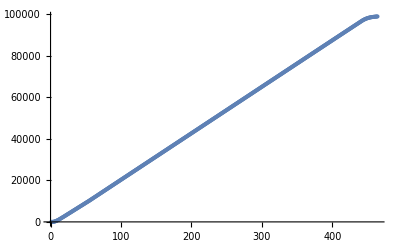

```mathematica
ListPlot[t2]
```

```mathematica
LinearModelFit[t2,x,x]
```

FittedModel[-1803.99+222.299 x]

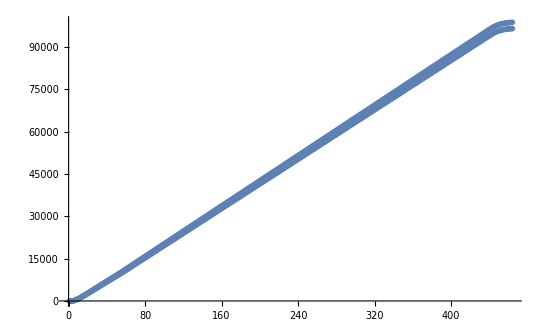

```mathematica
Show[ListPlot[t2],ListPlot[t]]
```